Exact Pole Position (k_res): 4.7143-0.0506794 ⅈ

(4.93168 (1+4 Re[(4.02158+0.999991 ⅈ) ((-4.7143+0.0506794 ⅈ)+z)]))/(Abs[(-22.2221+0.477836 ⅈ)+z^2]^2)

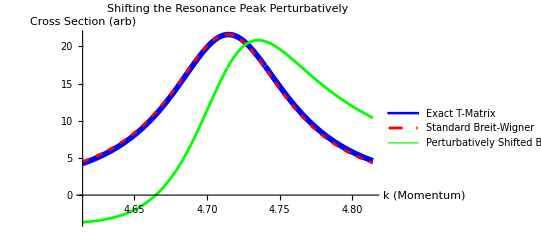

```mathematica
ClearAll["Global`*"]

(*1. Parameters*)
l=1;
μ=1;
a=1;
λ=20; (*Strong coupling to ensure resonance is sharp*)

(*2. Define the Exact T-Matrix Denominator*)
(*We use this to find the pole and calculate the exact cross section*)
Denom[k_]:=1-I*k*λ*a^2*SphericalBesselJ[l,k*a]*SphericalHankelH1[l,k*a];

(*3. Find the Exact Pole (k_res)*)
(*We search near the expected location*)
searchGuess=4;
root=FindRoot[Denom[k]==0,{k,searchGuess}];
kres=k/. root;

(*Output the pole location*)
Print["Exact Pole Position (k_res): ",kres]

(*4. Define Cross Sections*)

(*A.Exact Cross Section (Normalized to match peak height approx)*)
(*T~1/Denom.Sigma~ |T|^2*)
SigmaExact[k_]:=Abs[1/Denom[k]]^2;

(*B.Standard Breit-Wigner (Centered at k_res)*)
(*We normalize it to match the Exact sigma at the real part of the pole for comparison*)
NormFactor=SigmaExact[Re[kres]]*Abs[Re[kres]^2-kres^2]^2;
SigmaBW[k_]:=NormFactor/Abs[k^2-kres^2]^2;

(*C.Perturbative Correction (The Shift)*)
(*Calculate the slope S=Psi'/Psi at the pole*)
(*For delta shell,Psi(k) is just j_l(ka)*)
Psi[k_]:=SphericalBesselJ[l,k*a];
SlopeS=(D[Psi[k],k]/. k->kres)/Psi[kres];

(*The Formula:BW*(1+4 Re[(k-kres)*Slope])*)
SigmaPerturbative[k_]:=SigmaBW[k]*(1+4*Re[(k-kres)*SlopeS]);
SigmaPerturbative[z]

(*5. Visualization*)
PlotRangeMin=Re[kres]-0.1;
PlotRangeMax=Re[kres]+0.1;

Plot[{SigmaExact[k],SigmaBW[k],SigmaPerturbative[k]},{k,PlotRangeMin,PlotRangeMax},PlotStyle->{{Blue,Thickness[0.01]},(*Exact:Thick Blue*){Red,Dashed},(*Standard BW:Dashed Red*){Green,Thickness[0.005]}     (*Perturbative:Thin Green*)},PlotLegends->{"Exact T-Matrix","Standard Breit-Wigner","Perturbatively Shifted BW"},AxesLabel->{"k (Momentum)","Cross Section (arb)"},PlotLabel->"Shifting the Resonance Peak Perturbatively"]
```